# the workload test part 2

```mathematica
SetDirectory[NotebookDirectory[]];
rl[d_]:=Placed[d,Axis,Rotate[#,Pi/2]&]
SwapLoad[file_String]:=Import["../dataset/"<>file][[3;;All,5]]
VMLoad[file_String]:=Import["../dataset/"<>file][[4;;,{3,5,7}]]
TableLoad[f_,c_Integer]:=Table[f[ToString[i]],{i,1,c}]
MakeList[l1_List,l2_List,direction_List]:=Table[{1,
If[direction[[i]]>0,l2[[i]]/l1[[i]],l1[[i]]/l2[[i]]]}
,{i,Length[direction]}]
```

## dynamic tau redo all test

### 3-8 dynamic tau

key | value | key | value
N | 5GB | init mem | 512MB
VM count | 10 | f | 150MB
high load | 200MB | □ | □

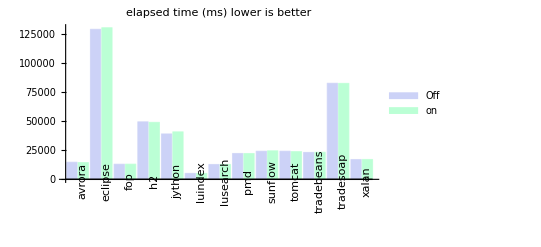

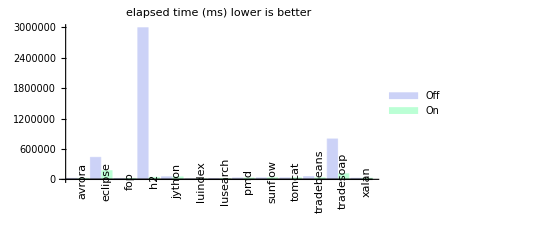

(ms) | off | on
avrora | 18238 | 17358
eclipse | 433186 | 171196
fop | 16029 | 17748
h2 | 2991145 | 37778
jython | 49847 | 47796
luindex | 6268 | 6144
lusearch | 15821 | 16029
pmd | 27475 | 26530
sunflow | 29067 | 30805
tomcat | 29034 | 29370
tradebeans | 54152 | 29416
tradesoap | 796455 | 110001
xalan | 21351 | 22948
sum | 4488068 | 563119

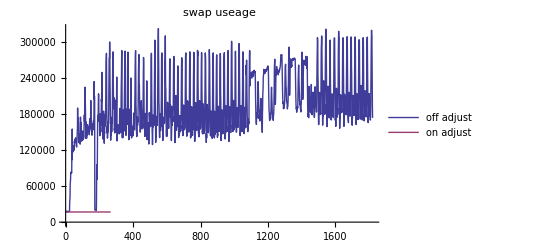

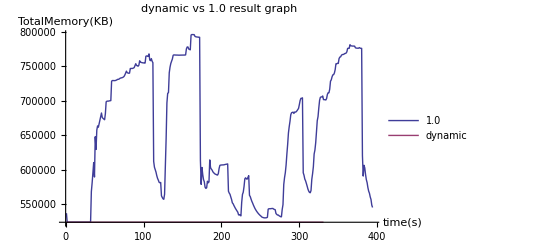

```mathematica
dp=Import["../dataset/3-8_dacapo/dacapo.ods"][[1]];
swapoff=SwapLoad["3-8_dacapo/off-swap.log"];
swapon=SwapLoad["3-8_dacapo/on-swap.log"];
hi=VMLoad["3-8_dacapo/high-2.log"];
low=VMLoad["3-8_dacapo/low-2.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
BarChart[dp[[2;;-2,4;;5]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","On"},PlotLabel->"elapsed time (ms) lower is better"]
Grid[dp[[All,{1,4,5}]],Frame->All]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,1]],low[[All,1]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon,hi,low]
```

配置512MB内存,运行时间相差非常大,而且几乎无法看到开启调节的柱状图.
而且SWAP分区使用率也是非常的夸张.
这个只能说是对于人而言.没有美观的感觉.但是对于系统而言是正常的结果.
我们需要接受它,当然.在论文中不使用这组数据.

### 3-9 dynamic tau high

key | value | key | value
N | 10GB | init mem | 1GB
VM count | 10 | f | 150MB
high load | 800MB | □ | □

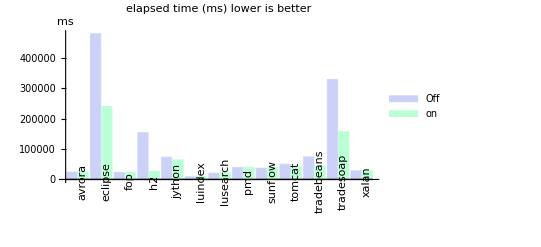

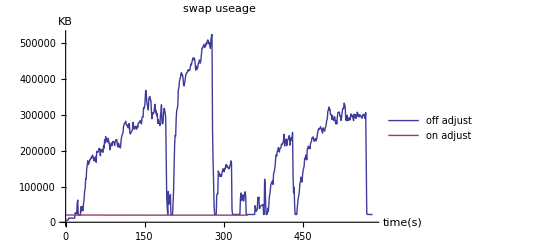

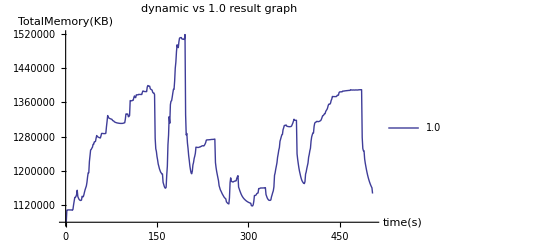

```mathematica
dp=Import["../dataset/3-9_dacapo_high/dacapo.ods"][[1]];
swapoff=SwapLoad["3-9_dacapo_high/off-swap.log"];
swapon=SwapLoad["3-9_dacapo_high/on-swap.log"];
hi=VMLoad["3-9_dacapo_high/high-10.log"];
BarChart[dp[[2;;-2,2;;3]],
ChartLabels->{rl[dp[[2;;-2,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better",
AxesLabel->"ms"
]
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",AxesLabel->{"time(s)","KB"},
PlotLegends->{"off adjust","on adjust"}]
ListLinePlot[{hi[[All,1]]},
PlotLegends->{"1.0","dynamic"},AxesLabel->{"time(s)","TotalMemory(KB)"},PlotLabel->"dynamic vs 1.0 result graph"]
Clear[dp,swapoff,swapon,hi]
```

结论和以前的类似.

## multi vm test

### 测试方法

首先分为两个大组,一个大组是开启调节的测试,一个大组是关闭调节的测试.
每个大组安排每个虚拟机上运行不同性质的测试.为了保证满足调节条件.需要安排
每个大组至少有一台以上的vm运行内存密集程序,称为目标机.至少有一台以上的vm运行非内存密集程序
(如CPU密集和磁盘密集).为了使得运行非内存密集的vm把内存贡献给目标机.
同时,每台vm在测试的时候还需要执行记录swap的程序.在开启调节的时候需要记录每台虚拟机分配的内存.

内存型密集程序可以选择dacapo测试集中的h2,...因为目前只找到dacapo测试集的这几个测试属于内存密集型.
非内存密集型可以选择phoronix-test-suite测试框架中的许多程序如:
nginx
...

因为每个测试运行的时间都不一样.所以规定以单次测试时间最长的测试所运行的时间作为该大组测试的时间.
对于单次运行时间不足的测试采用循环运行的方式.当运行时间超过该大组的测试时间时候强制手工杀死测试进程.
因为最后一次运行时间不足一个完整的周期所以该次测试成绩无效.对于之前运行的所有测试成绩(包括循环运行的所有有效成绩)取平均值作为该项测试的成绩.

因为每组测试间单位不同，没有比较的意义。所以
最后将两大组的每个测试的成绩相除,换算成百分比.以不开启调节为基准1.因为一些测试成绩是越高越好,一些成绩是越低越好.
所以需要注意除以的方向

### 3-22 2vm test

N | 1G | init men | 512MB
vmcount | 2 | f | 120M
vm1 | nginx | high load | 0
vm2 | h2 | high load | 100MB

| vm1 | vm2
 | nginx | h2
unit | request/s | ms
off | 6589.78 | 110753
on | 6488.57 | 42207

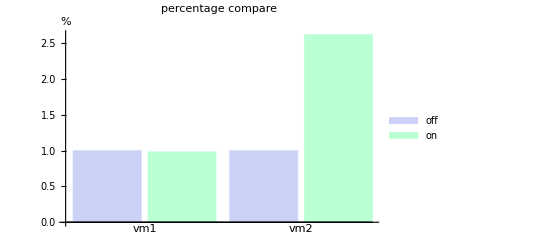

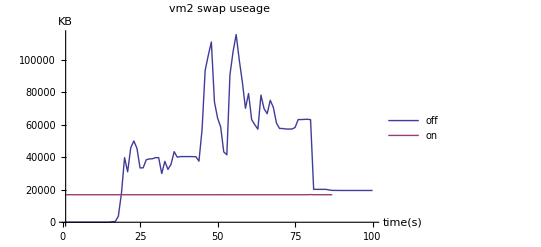

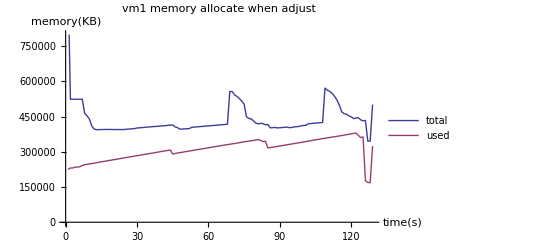

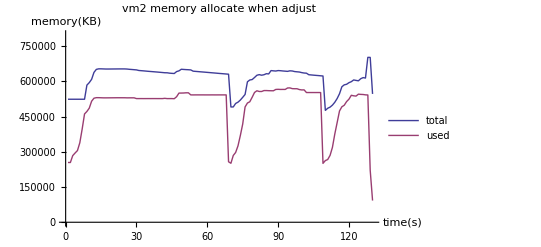

```mathematica
table=Import["../dataset/3-22/statics.ods"][[1]];
offswap={None,SwapLoad["3-22/vm2/off-swap.log"]};
onswap={SwapLoad["3-22/vm1/on-swap.log"],SwapLoad["3-22/vm2/on-swap.log"]};
onmem={VMLoad["3-22/vm1/on.log"],VMLoad["3-22/vm2/on.log"]};
Grid[table[[1;;-2]],Frame->All]
BarChart[{{1,table[[5,2]]/table[[4,2]]},{1,table[[4,3]]/table[[5,3]]}},
PlotLabel->"percentage compare",ChartLegends->{"off","on"},
ChartLabels->{{"vm1","vm2"},None},AxesLabel->"%"
]
ListLinePlot[{offswap[[2,1;;-40]],onswap[[2]]},
PlotRange->All,PlotLabel->"vm2 swap useage ",PlotLegends->{"off","on"},
AxesLabel->{"time(s)","KB"}
]
ListLinePlot[{onmem[[1,All,1]],onmem[[1,All,2]]},
PlotRange->{0,800000},PlotLabel->"vm1 memory allocate when adjust",
PlotLegends->{"total","used"},AxesLabel->{"time(s)","memory(KB)"}
]
ListLinePlot[{onmem[[2,All,1]],onmem[[2,All,2]]},
PlotRange->{0,800000},PlotLabel->"vm2 memory allocate when adjust",
PlotLegends->{"total","used"},AxesLabel->{"time(s)","memory(KB)"}
]
Clear[table,offswap,onswap,onmem]
```

对于两台虚拟机的测试,可以看到结果是类似的.主要依然表现为以下几个方面:
图1:
-    对于非内存密集型的程序.性能会有所下降.但是下降的数量不大.
-    对于内存密集型的程序.因为保证了分配足够的内存.所以相对于不开启调节的性能有提升许多
图2:
-    不开启调节的vm2占用大量的swap.(vm1因为不需要太多内存,所以始终没有使用swap).
-    开启了调节之后vm2就不再使用swap了.(从途中可以看到swap一直保持一个数,这是因为不开启调节的测试是紧接着上一个测试的)
-    两者运行的时间相差无几.这是因为整个测试以最长的时间为基准(vm1上单次运行需要的时间)
      vm2上其实完整的执行了2次
图3,图4:
-   对于vm1可以看到,分为3个阶段.其实是3次测试,phoronix-test-suite默认运行3次求平均值作为最后结果.
    三次测试内存需求逐渐升高.
-   对于vm2可以看到,分为2个完整的测试和一个不完整的测试.因为dacapo只运行1次.所以当第一次运行结束之后,
    就通过外部的脚本的循环,进行下一个周期,而且明显的可以看到第二次运行的时间比第一次短得多.关于这一点目前还没有能力解释.
    当第3次还没有运行完成之后.vm1就结束了.所以这里手工杀死测试进程.
    
2台虚拟机的测试还不能说明什么问题.
下面的5台虚拟机和10台虚拟机能够更加深刻的说明问题.

### 03-24 5vm test

N | 2.5G | init men | 512MB
vmcount | 5 | f | 120M

安排5台虚拟机,每台虚拟机都循环运行一个测试,每个测试的参数如下:

vm | test | intensive | high load | unit
vm1 | nginx | cpu | 0 | Reqeust/s
vm2 | tradebeans | mem | 100MB | ms
vm3 | build-mplayer | cpu | 0 | s
vm4 | tradesoap | mem | 100MB | ms
vm5 | pgbench | disk | 0 | Transaction/s

```mathematica
{table,offraw,onraw}=Import["../dataset/3-24/statics.xlsx"];
offswap=TableLoad[SwapLoad["3-24/vm"<>#<>"/off-swap.log"]&,5];
onswap=TableLoad[SwapLoad["3-24/vm"<>#<>"/on-swap.log"]&,5];
onmem=TableLoad[VMLoad["3-24/vm"<>#<>"/on-mem.log"]&,5];
```

如图:下面是取平均之后的测试结果表格

```mathematica
Grid[table[[1;;-2]],Frame->All]
```

id | nginx | tradebeans | build-mplayer | tradesoap | pgbench
intensive | cpu | mem | cpu | mem | disk
unit | request/s | ms | s | ms | TPS
off | 6432.33 | 26163.6 | 576.933 | 109978. | 93.55
on | 6103.59 | 25830. | 626.16 | 95930.8 | 118.493

为了更清楚的看到它们的比例,下面画出条形图:

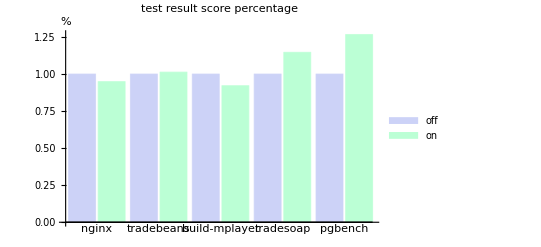

```mathematica
BarChart[MakeList[table[[4,2;;]],table[[5,2;;]],{1,-1,-1,-1,1}],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{table[[1,2;;]],None},AxesLabel->"%"
]
```

可以看到测试成绩提高依次排序为pgbench>tradesoap>tradebeans.
其中tradebeans和tradesoap都是内存密集型程序.符合我们的预期.
但是反而pgbench磁盘密集型程序提高最多.比较难于理解.

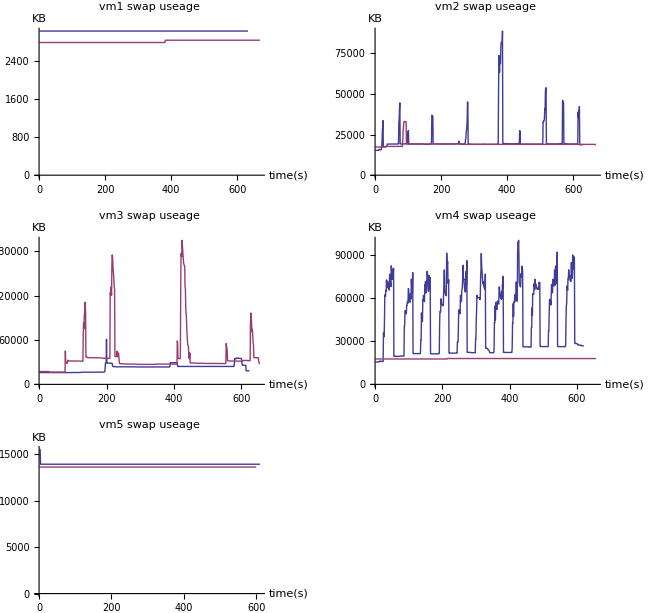

```mathematica
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
```

因为我们主要关心swap的情况,我们可以看到,除了build-mplayer测试开启调节后swap的使用量上升之外,
其他测试的swap使用量都减小到了合理的程度.特别是对于vm4效果非常明显.这也是vm4提分比较多的原因.
可以说明调节程序是基本达到了我们预期的效果.
编译程序的swap的反常其实是因为编译程序的内存使用是脉冲形状,在一小段时间里内存使用量迅速增加又迅速减小,超过了调节的精度.所以无法调节.
最后,磁盘密集型程序得分也高的原因,可以做一个猜想,因为之前大量的使用swap,导致I/O量大,磁盘工作不过来.而之后基本不使用swap了,磁盘能够集中精力处理pgbench的请求.所以分数也高了.

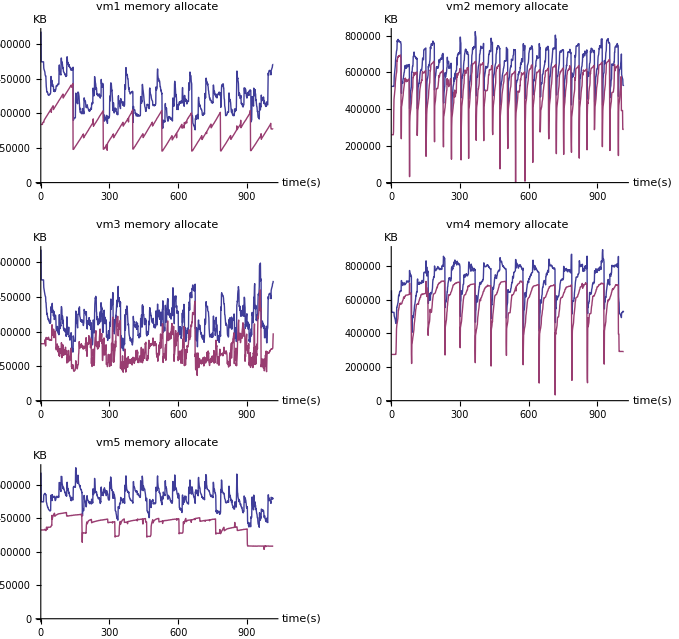

```mathematica
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

#### 附录:

关闭调节各个测试的详细分数列表:

```mathematica
Grid[offraw,Frame->All]
```

nginx | tradebeans | build-mplayer | tradesoap | pgbench
6404.01 | 25947. | 589.77 | 115837. | 98.12
6468.04 | 25913. | 569.91 | 104774. | 93.38
6470.55 | 27493. | 571.12 | 111566. | 89.96
6380.12 | 26646. |  | 114275. | 92.13
6533.53 | 25818. |  | 108938. | 94.16
6542.23 | 27082. |  | 114150. | 
6416.12 | 24898. |  | 110295. | 
6439.23 | 25631. |  | 119415. | 
6443.25 | 26037. |  | 102577. | 
6305.37 | 27581. |  | 105173. | 
6366.04 | 25591. |  | 102755. | 
6285.7 | 25440. |  |  | 
6511.87 | 25840. |  |  | 
6361.72 | 26198. |  |  | 
6428.31 | 25994. |  |  | 
6417.03 | 25997. |  |  | 
6516.57 | 25709. |  |  | 
6492.19 | 25550. |  |  | 
 | 25574. |  |  | 
 | 25448. |  |  | 
 | 28754. |  |  | 
 | 26459. |  |  |

开启调节后各个测试的详细分数表

```mathematica
Grid[onraw,Frame->All]
```

nginx | tradebeans | build-mplayer | tradesoap | pgbench
6040.82 | 27091. | 647.74 | 96508. | 113.29
5983.04 | 26628. | 622.26 | 97406. | 119.
6025.34 | 26376. | 608.48 | 97223. | 125.21
6009.15 | 26717. |  | 95176. | 123.13
6006.31 | 26808. |  | 95332. | 105.15
5946.25 | 26435. |  | 94357. | 125.18
6072.94 | 26654. |  | 95454. | 
6321.03 | 27436. |  | 96337. | 
6244.55 | 26446. |  | 95850. | 
6128.24 | 27611. |  | 95505. | 
6045.95 | 25585. |  | 95847. | 
6033.12 | 26875. |  | 95549. | 
6213.83 | 26058. |  | 96557. | 
6346.85 | 26809. |  |  | 
6364.43 | 25642. |  |  | 
6056.4 | 27181. |  |  | 
5972.76 | 2611. |  |  | 
6053.62 | 27475. |  |  | 
 | 26200. |  |  | 
 | 27609. |  |  | 
 | 25984. |  |  | 
 | 27521. |  |  | 
 | 25880. |  |  | 
 | 26752. |  |  | 
 | 26638. |  |  | 
 | 27899. |  |  | 
 | 26923. |  |  | 
 | 25396. |  |  |

### 03-27; 5vm test again

重新测试了一遍5vm的.得到类似的结论.到时候取一组即可.

```mathematica
{table,offraw,onraw}=Import["../dataset/3-27/statics.xlsx"];
offswap=TableLoad[SwapLoad["3-27/vm"<>#<>"/off-swap.log"]&,5];
onswap=TableLoad[SwapLoad["3-27/vm"<>#<>"/on-swap.log"]&,5];
onmem=TableLoad[VMLoad["3-27/vm"<>#<>"/on-mem.log"]&,5];
```

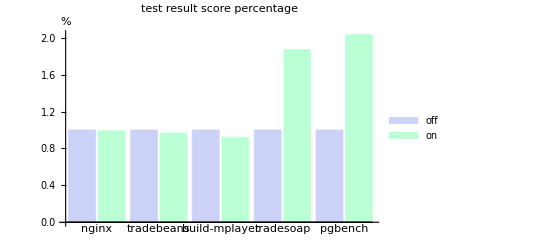

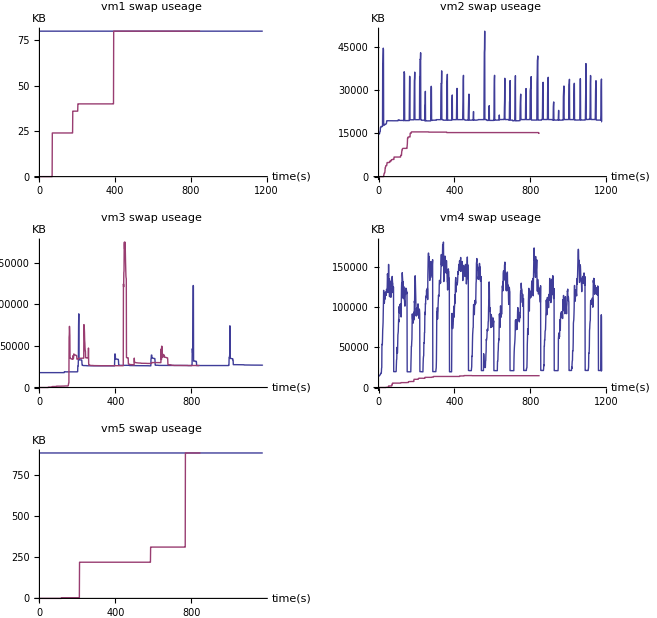

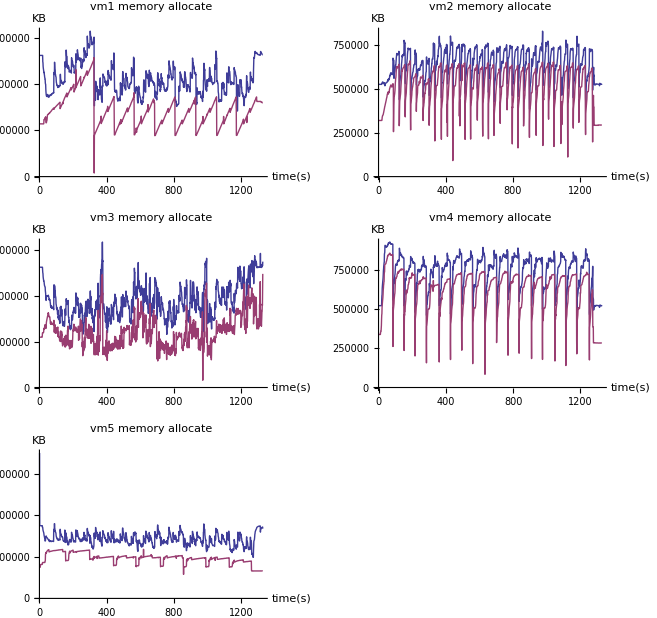

```mathematica
BarChart[MakeList[table[[4,2;;]],table[[5,2;;]],{1,-1,-1,-1,1}],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{table[[1,2;;]],None},AxesLabel->"%"
]
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

### 04-01;10 vm

N | 5G | init men | 512MB
vmcount | 10 | f | 120M

安排10台虚拟机,每台虚拟机都循环运行一个测试,每个测试的参数如下:

vm | test | intensive | high load | unit
vm1 | apache | cpu | 0 | Reqeust/s
vm2 | h2 | mem | 100MB | ms
vm3 | build-linux-kernel | cpu | 0 | s
vm4 | tradebeans | mem | 100MB | ms
vm5 | pgbench | disk | 0 | Transaction/s
vm6 | tradesoap | □ | □ | □
vm7 | john-the-ripper | □ | □ | □
vm8 | scimark2 | □ | □ | □
vm9 | openssl | □ | □ | □
vm10 | crafty | □ | □ | □

```mathematica
{table,offraw,onraw}=Import["../dataset/4-01/statics.xlsx"];
label=table[[1,{2,3,4,5,6,7,8,11,17,18}]];
offswap=TableLoad[SwapLoad["4-01/vm"<>#<>"/off-swap.log"]&,10];
onswap=TableLoad[SwapLoad["4-01/vm"<>#<>"/on-swap.log"]&,10];
onmem=TableLoad[VMLoad["4-01/vm"<>#<>"/on-mem.log"]&,10];
```

```mathematica
Grid[table[[1;;-2]]ᵀ,Frame->All]
```

id | sub id | intensive | load | unit | off | on
apache |  | cpu | 0. | request/s | 2702.31 | 2632.62
h2 |  | mem | 0. | ms | 123209. | 32645.5
Build-linux-kernel |  | cpu | 0. | s | 1061.81 | 1197.62
tradebeans |  | mem | 100M | ms | 26426. | 28727.5
pgbench |  | disk | 0. | TPS | 88.091 | 109.003
tradesoap |  | mem | 100M | ms | 111204. | 100578.
John-the-ripper | Blowfish | cpu | 0. | real C/S | 546. | 530.
 | Traditional DES | cpu | 0. | real C/S | 1.87267×10^6 | 2.01667×10^6
 | MD5 | cpu | 0. | real C/S | 17724. | 16572.2
scimark2 | Composite | cpu | 100M | Mflops | 423.273 | 391.655
 | Monte Carlo | cpu | 100M | Mflops | 161.595 | 161.498
 | Fast Fourier Transform | cpu | 100M | Mflops | 38.2575 | 33.7475
 | Sparse Matrix Multiply | cpu | 100M | Mflops | 482.323 | 382.73
 | Dense LU Matrix Factorization | cpu | 100M | Mflops | 997.03 | 951.218
 | Jacobi Successive Over-Relaxation | cpu | 100M | Mflops | 431.89 | 428.423
openssl |  | cpu | 0. | score | 52.0162 | 51.9261
crafty |  | cpu | 0. | s | 220.058 | 217.493

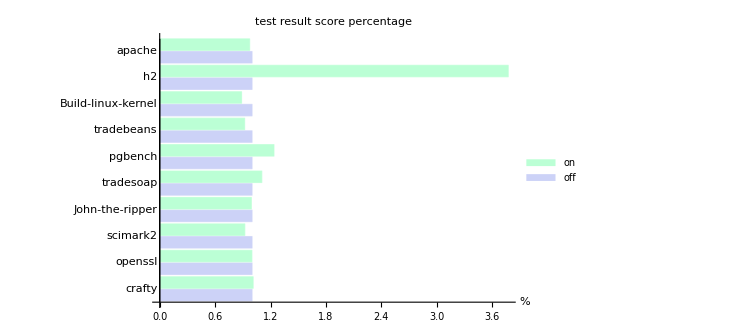

```mathematica
bar=
MakeList[table[[6,2;;7]],table[[7,2;;7]],{1,-1,-1,-1,1,-1}]~
Join~
{
{1,GeometricMean[table[[7,8;;10]]/table[[6,8;;10]]]},
{1,GeometricMean[table[[7,11;;16]]/table[[6,11;;16]]]}
}~
Join~
MakeList[table[[6,17;;18]],table[[7,17;;18]],{1,-1}];
BarChart[Reverse[bar],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{Reverse[label],None},AxesLabel->"%",BarOrigin->Left
]
```

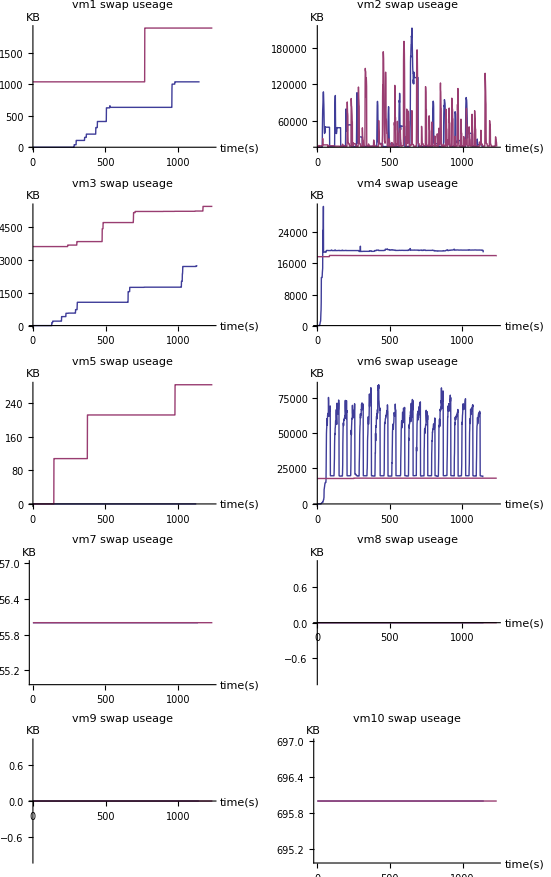

```mathematica
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->All,PlotLabel->"vm"<>ToString[i]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
```

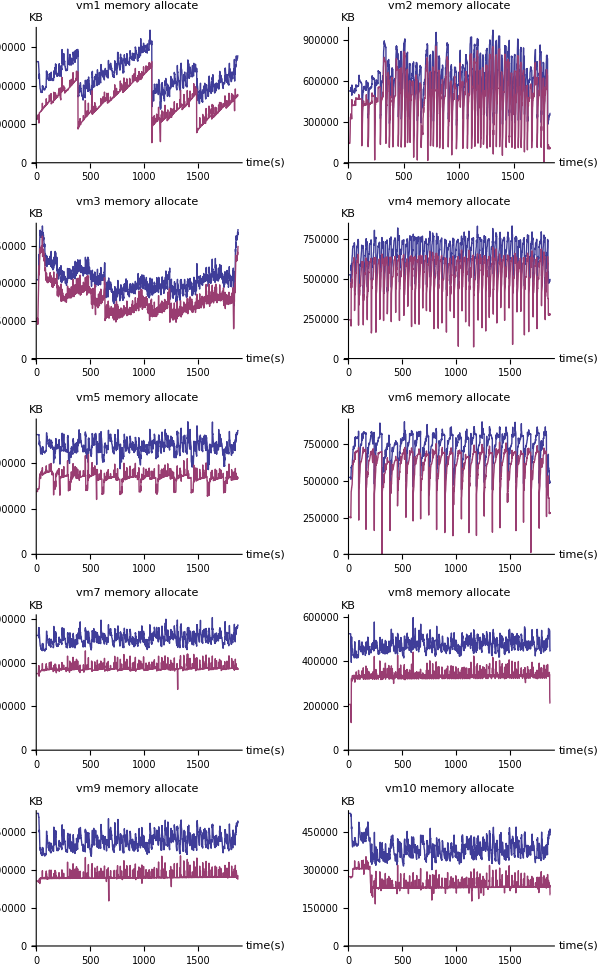

```mathematica
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->"vm"<>ToString[i]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

### 04-03 10 vm again

N | 5G | init men | 512MB
vmcount | 10 | f | 120M

安排10台虚拟机,每台虚拟机都循环运行一个测试,每个测试的参数如下:

vm | test | intensive | high load | unit
vm1 | apache | cpu | 0 | Reqeust/s
vm2 | h2 | mem | 0 | ms
vm3 | build-linux-kernel | cpu | 0 | s
vm4 | tradebeans | mem | 100MB | ms
vm5 | pgbench | disk | 0 | Transaction/s
vm6 | tradesoap | mem | 100MB | ms
vm7 | john-the-ripper | cpu | 0 | real C/S
vm8 | scimark2 | cpu | 100MB | Mflops
vm9 | openssl | cpu | 0 | score
vm10 | crafty | cpu | 0 | s

```mathematica
{table,offraw,onraw}=Import["../dataset/4-02/statics.xlsx"];
label=table[[1,{2,3,4,5,6,7,8,11,17,18}]];
offswap=TableLoad[SwapLoad["4-02/vm"<>#<>"/off-swap.log"]&,10];
onswap=TableLoad[SwapLoad["4-02/vm"<>#<>"/on-swap.log"]&,10];
onmem=TableLoad[VMLoad["4-02/vm"<>#<>"/on-mem.log"]&,10];
```

```mathematica
Grid[table[[1;;-2]]ᵀ,Frame->All]
```

id | sub id | intensive | load | unit | off | on
apache |  | cpu | 0. | request/s | 2987.47 | 2666.06
h2 |  | mem | 0. | ms | 120342. | 32328.3
Build-linux-kernel |  | cpu | 0. | s | 1057.5 | 1203.63
tradebeans |  | mem | 100M | ms | 25991.2 | 28541.1
pgbench |  | disk | 0. | TPS | 88.8258 | 103.918
tradesoap |  | mem | 100M | ms | 104163. | 102019.
John-the-ripper | Blowfish | cpu | 0. | real C/S | 564. | 530.333
 | Traditional DES | cpu | 0. | real C/S | 2.297×10^6 | 2.02833×10^6
 | MD5 | cpu | 0. | real C/S | 18196. | $Failed
scimark2 | Composite | cpu | 100M | Mflops | 410.125 | 408.655
 | Monte Carlo | cpu | 100M | Mflops | 161.74 | 159.443
 | Fast Fourier Transform | cpu | 100M | Mflops | 41.06 | 40.735
 | Sparse Matrix Multiply | cpu | 100M | Mflops | 451.07 | 449.98
 | Dense LU Matrix Factorization | cpu | 100M | Mflops | 974.828 | 961.228
 | Jacobi Successive Over-Relaxation | cpu | 100M | Mflops | 431.435 | 430.075
openssl |  | cpu | 0. | score | 52.0355 | 51.9184
crafty |  | cpu | 0. | s | 192.138 | 215.855

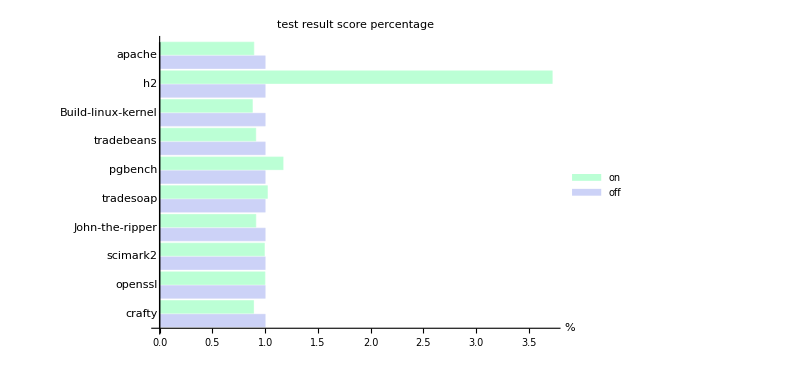

```mathematica
bar=
MakeList[table[[6,2;;7]],table[[7,2;;7]],{1,-1,-1,-1,1,-1}]~
Join~
{
{1,GeometricMean[table[[7,8;;9]]/table[[6,8;;9]]]},
{1,GeometricMean[table[[7,11;;16]]/table[[6,11;;16]]]}
}~
Join~
MakeList[table[[6,17;;18]],table[[7,17;;18]],{1,-1}];
BarChart[Reverse[bar],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{Reverse[label],None},AxesLabel->"%",BarOrigin->Left
]
```

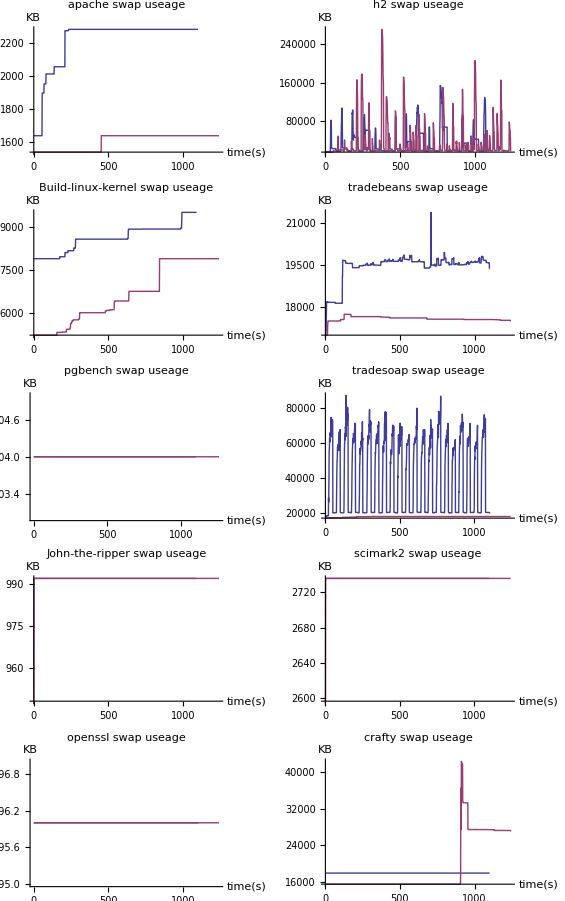

```mathematica
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->All,PlotLabel->label[[i]]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2,2,1,{}]]
```

从结果上可以看出:除了h2,tradebeans,tradesoap三个测试是大量的使用SWAP交换空间,其它的测试都没有使用交换空间.

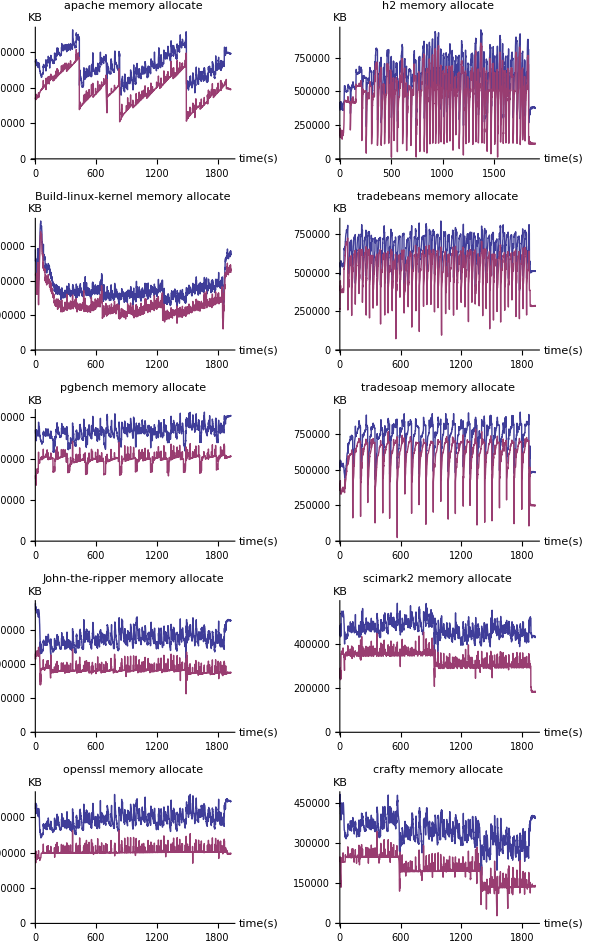

```mathematica
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->label[[i]]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

### 04-16 10 vm final

一共测试了3次,使用第三次结果.

N | 5G | init men | 512MB
vmcount | 10 | f | 120M

安排10台虚拟机,每台虚拟机都循环运行一个测试,每个测试的参数如下:

vm | test | intensive | high load | unit
vm1 | apache | cpu | 0 | Reqeust/s
vm2 | h2 | mem | 0 | ms
vm3 | build-linux-kernel | cpu | 0 | s
vm4 | tradebeans | mem | 100MB | ms
vm5 | pgbench | disk | 0 | Transaction/s
vm6 | tradesoap | mem | 100MB | ms
vm7 | john-the-ripper | cpu | 0 | real C/S
vm8 | scimark2 | cpu | 100MB | Mflops
vm9 | system-libxml2 | cpu | 0 | ms
vm10 | compress-7zip | cpu/mem | 10MB | MIPS

选取这样10个测试是经过仔细考虑的,主要基于以下因素:

1. 尽可能的覆盖各种类型的测试
2. 体现实际服务器的各种用途的不同内存需求
3. 为了使得内存使用量区别开来,随机安排一些虚拟机使用了负载程序.
4. 为了能够顺利完成测试，需要根据实际情况调节负载程度。
4. 不同时使用两个磁盘密集型程序,是为了保持测试能够顺利完成,当使用两个磁盘密集型程序之后,
    两个程序互相拖累,造成时间大幅度延长,两个测试分数对比开启调节之后都非常的低.
5. 虚拟机cpu是完全独立的分配的,所以测试项目的数量对整个结果没有影响.这个说法的前提是
    我们测试环境物理机CPU有64核心，为了降低CPU对实验的影响我们限制每台虚拟机均模拟成
    单核CPU，于是每个虚拟机都平均跑在物理机的一个核心上，所以CPU成为互相独立的环境了。

我们选择了dacapo测试中表现比较好的部分测试和phoronix-test-suite中的许多测试，
涵盖了cpu，内存，磁盘等多方面的性能对比，具有实际指导意义。

下面是对各种测试的说明

[对测试程序的说明](../test.md)

本来dacapo的测试结果已经十分有力地说明了开启调节对于内存型的程序有利这一事实，
但是dacapo测试都是java程序，不得不使我们提出，是否因为java虚拟机普遍不节约内存，
是否结论对于更一般的c语言程序，系统程序也适用的疑问。

为此，我们在接下来的多vm测试中，特地选用了phoronix-test-suite测试套件，提供了丰富
的测试程序的选择，并且phoronix-test-suite具有很多优点，免费跨平台，其他人能够非常方面的
重现测试。

唯一一点具有争议地是，phoronix-test-suite使用了系统源中的库，我们知道SPEC测试权威，严谨
体现在，它所使用的测试甚至连编译测试的工具都是需要编译的，相同的代码保证了测试成绩减少了
因为更新的库版本所带来的性能优化的干扰。

而phoronix-test-suite使用了系统的包管理器来安装依赖库这点，一是简化自身复杂度，但是的确带来了
配置相同，系统版本不同的两个环境的分数的比较会引入实验误差。但是所带来的优势也是巨大的。
一是方便快速部署测试环境。因为同样的SPEC2000因为编译编译工具失败而无法使用，即使程序完全是独立的。
二是因此更接近真实环境。因为实际生产环境中现在的系统肯定是使用的系统源里面的库，
很难想象一个2010年的系统使用10年前的库版本进行测试和在实际生产中使用的库的性能差距的鸿沟。

（也不是故意黑SPEC，不过真的对编译失败感到非常的不爽）
即，SPEC的测试成绩用来相互比较具有优势，phoronix-test-suite的测试成绩更接近实际的性能。
两者个有利弊。

因为phoronix-test-suite的这点的特殊性，十分有必要做出说明，和我们选择后可能带来的问题。

另外，需要特别说明的是，测试中使用了6个占用内存巨大的程序，1个内存中等，3个内存较小的程序。
3台虚拟机开启内存负载程序，1台虚拟机使用微量内存负载设置。
实际测试中，动态τ长期达到1,是完全的并且基本上是包括全部虚拟机的整体高负荷环境。
内存变化剧烈，完全靠自然地时分原理将测试内存错开使用，从而达到提高内存型测试地整体分数，
并且得益于减少SWAP的使用，即减少磁盘动作，所以同时提高了磁盘测试的分数。

同时，因为这种动荡的测试环境，测得的分数也经常发生变化，标准差的偏差经常发生变动，

主要表现在：
对相同的测试组合进行多次测试，测得的分数偏差不大，可以参考10vm的前两组测试对比和5vm的前两组测试对比。
所以同一组合内的分数对比是可行的，

一旦测试组合发生小范围变动，测试的分数对于之前的测试组合，分数偏差都比较大，可以参考10vm的2,和3次测试。
所以对于不同组合的分数对比是不可行的。因为不同的测试就算cpu是完全隔离的，磁盘和内存都是相互关联的。很可
能增加了一个内存密集型程序，在不开启调节的时候使用SWAP，增大IO，从而拉低磁盘程序的分数。

所以，不能简单的根据分数说磁盘型的开启调节比不开启调节性能提升30%,

但是，就算分数变动的存在，得分百分比的趋势也是相同的。开启调节有利于磁盘型和内存型测试的运行
的事实是不可否认的。

所以，我们使用“磁盘型的开启调节比不开启调节性能提升巨大/显著”的说法是可行的。

```mathematica
{table,offraw,onraw}=Import["../dataset/4-16/statics.xlsx"];
label=table[[1,{2,3,4,5,6,7,8,11,17,18}]];
offswap=TableLoad[SwapLoad["4-16/vm"<>#<>"/off-swap.log"]&,10];
onswap=TableLoad[SwapLoad["4-16/vm"<>#<>"/on-swap.log"]&,10];
onmem=TableLoad[VMLoad["4-16/vm"<>#<>"/on-mem.log"]&,10];
```

以下是各个测试的具体成绩.
其中john-the-ripper有3组,
scimark2有6组子子测试.

```mathematica
Grid[table[[1;;-2]]ᵀ,Frame->All]
```

id | sub id | intensive | load | unit | off | on
apache |  | cpu | 0. | request/s | 2997.03 | 2625.55
h2 |  | mem | 0. | ms | 136755. | 25365.2
Build-linux-kernel |  | cpu | 0. | s | 1111.55 | 1265.71
tradebeans |  | mem | 100M | ms | 25881.8 | 26403.2
pgbench |  | disk | 0. | TPS | 39.8787 | 105.675
tradesoap |  | mem | 100M | ms | 135685. | 111958.
John-the-ripper | Blowfish | cpu | 0. | real C/S | 542. | 550.
 | Traditional DES | cpu | 0. | real C/S | 2.19983×10^6 | 2.206×10^6
 | MD5 | cpu | 0. | real C/S | 16546. | 18172.
scimark2 | Composite | cpu | 100M | Mflops | 397.503 | 400.235
 | Monte Carlo | cpu | 100M | Mflops | 161.68 | 161.528
 | Fast Fourier Transform | cpu | 100M | Mflops | 36.278 | 36.7225
 | Sparse Matrix Multiply | cpu | 100M | Mflops | 420.94 | 441.843
 | Dense LU Matrix Factorization | cpu | 100M | Mflops | 923.814 | 953.023
 | Jacobi Successive Over-Relaxation | cpu | 100M | Mflops | 430.304 | 430.375
System-libxml2 |  | cpu | 0. | ms | 171762. | 178210.
compress-7zip |  | cpu | 0. | MIPS | 1361.75 | 1480.25

为了方便观察.制作了条形统计图.
并且使用几何平均,将john-the-ripper和scimark2的多组数据进行了合并.

| off | on
apache | 1 | 0.876052
h2 | 1 | 5.39144
Build-linux-kernel | 1 | 0.878202
tradebeans | 1 | 0.980252
pgbench | 1 | 2.64992
tradesoap | 1 | 1.21193
John-the-ripper | 1 | 1.03776
scimark2 | 1 | 1.01644
System-libxml2 | 1 | 0.963822
compress-7zip | 1 | 1.08702

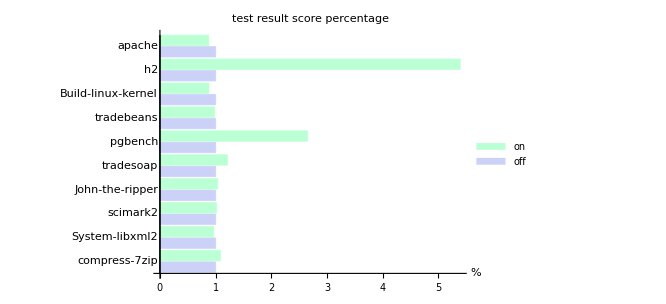

```mathematica
bar=
MakeList[table[[6,2;;7]],table[[7,2;;7]],{1,-1,-1,-1,1,-1}]~
Join~
{
{1,GeometricMean[table[[7,8;;10]]/table[[6,8;;10]]]},
{1,GeometricMean[table[[7,11;;16]]/table[[6,11;;16]]]}
}~
Join~
MakeList[table[[6,17;;18]],table[[7,17;;18]],{-1,1}];
TableForm[bar,TableHeadings->{label,{"off","on"}}]
BarChart[Reverse[bar],
PlotLabel->"test result score percentage",ChartLegends->{"off","on"},
ChartLabels->{Reverse[label],None},AxesLabel->"%",BarOrigin->Left
]
```

可以看到分数差距最明显的是h2测试,因为该测试是完全的内存密集型,内存的多少对程序的执行具有非常明显的速度影响.

其次比较明显的是pgbench测试,因为该测试是磁盘密集型,当不开启调节的时候,各个虚拟机都大量的使用交换空间,消耗I/O带宽.
所以开启调节之后测试成绩反而有比较明显的提高.
然后是tradesoap和compress-7zip，都带来了一定的提升，

还有的比如scimark2和john-the-ripper,因为对比上两次的测试结果，不能定论其结果就一定是优势地。

剩下的测试分数都有所降低,在10%的范围内.

特别地，尤其地，对于h2的夸张的有利测试结果需要做进一步的思考。和之前dacapo的测试对比，可以发现h2测试的
分数的确是提高几倍不假，但是是否是因为h2这个测试的特殊性，以及h2测试能否代表内存数据库的一般结果。因为
我们没有发现另外的某一个测试成绩能够达到h2如此好的结果，所以很难证明。我们只能得出一个大概的结论：
开启调节之后对内存数据库的哦影响程度巨大，这个巨大大概指的是50%~150%。但是不会是400%如此夸张。

另外，对比第3次实验结果和第2次实验结果。我们可以发现pgbench提升巨大。这是因为我们增加了一个内存密集型测试
compress-7zip,
在不开启调节的时候，内存密集型程序的内存代价都转化成了读写SWAP，即磁盘代价，所以拉低了pgbench的测试分数。
并且拉低明显。

虽然我们的条件中写到，不同时使用两个磁盘测试，也正是因为如此，两个磁盘测试互相拉低，最后造成测试成绩无意义。
甚至无法完成测试。

虽然我们有意的避免上面的现象，但是就算增加内存型的测试，也会在不开启调节的时候无意识的转化为对磁盘的代价输出。
很难保证独立性。所以要做出特别声明。

另外，我们也可以从测试中得出一些虚拟机布局的建议：即，不要在一台物理机上面的2台及以上的虚拟机部署磁盘型服务。
如同上面分析所示。
并且，如果是部署多台内存密集型服务，请使用一定地调节措施，会具有生产等级的优势。例如我们的内存调节程序。
对于CPU型服务，可以随便部署，不受约束。

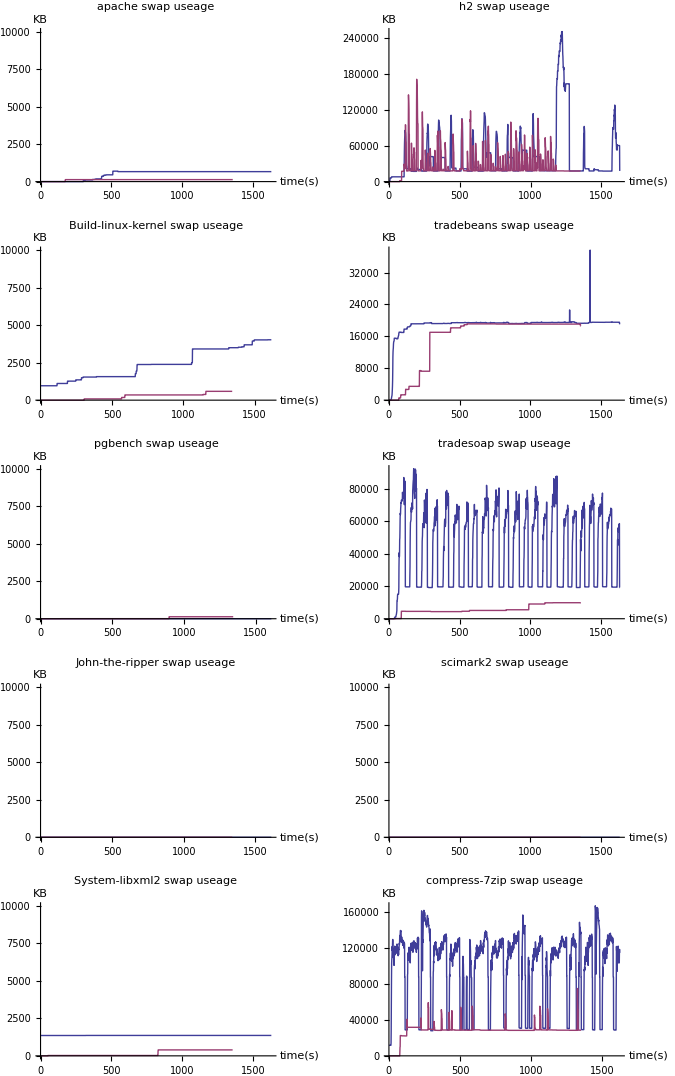

```mathematica
LineLegend[1,{"off","on"},LegendLayout->"Row"]
GraphicsGrid[Partition[
Table[
ListLinePlot[{offswap[[i]],onswap[[i]]},
PlotRange->{0,Max[10000,Max[offswap⟦i⟧]]},PlotLabel->label[[i]]<>" swap useage ",
AxesLabel->{"time(s)","KB"}],
{i,Length[offswap]}]
,2]]
```

从SWAP的使用量上分析我们也能够得到一些有趣的结论。
首先，只有h2,tradebeans,tradesoap,compress-7zip大量的使用了SWAP，也说明他们的确
具有非常明显的内存型特征。
剩下的因为使用SWAP内存量很少，所以我们直接忽略，需要注意的是，他们的y轴刻度都非常的小，
和内存型的不是一个数量级。需要特别注意。

另外，观察tradebeans的SWAP曲线，发现它逐渐增长到20MB就没有下降过，其他非内存的SWAP曲线也是
只升不降低，那么他们是不是就是一直在不断使用SWAP呢。

不是的。

我们可以观察剩下三个的SWAP曲线，发现他们的极小值都是非常的平。并且大概就在20MB左右。
加上我们知道不使用SWAP，SWAP的使用量会降低。
但是也不有不使用SWAP，SWAP的使用量不会回归到0的结论。

于是我们可以得到启示：linux的swap策略分为两个阶段。
1. 当SWAP使用量在阈值以下（大概20MB），SWAP只增不减。
2. 当SWAP使用量在阈值以上，SWAP能够真实的反应用量。

在前面我们讨论过，平衡公式不能引入SWAP，是因为
在1的情况，会有一个持续的虚假的正反馈，导致调节不断增大。
在2的情况，会引入震荡现象。
所以最后我们决定不使用SWAP。

但是如果我们有了以上的结论，我们就可以设计一个正确的SWAP模型，即，当SWAP使用量在20MB以下时候，直接忽略。
当SWAP在20MB以上的时候，引入公式，提供反馈，并且为了消除震荡现象，需要循环计算直到两次结果相差小于精度。

不过明显，我们在最后才拿到这个结论，所以时间已经不允许我们重新设计公式了。
并且我们有强力的动态τ调节，能够正确的调节。

但是，我们也应该注意到，如果加入SWAP进入公式，能够达到更好的效果。
能够避免一旦开始使用SWAP，内存用量不增加，所以总内存不变，所以额外的内存需求只能转化为SWAP输出。
即，一旦使用SWAP会持续使用SWAP的可能。

所以动态τ调节实际上是使用了“即使使用了SWAP，当内存需求提出后，内存用量也依然增加，从而分配更多的内存。
减缓全部内存需求转换为SWAP输出的趋势。”这样的断言。

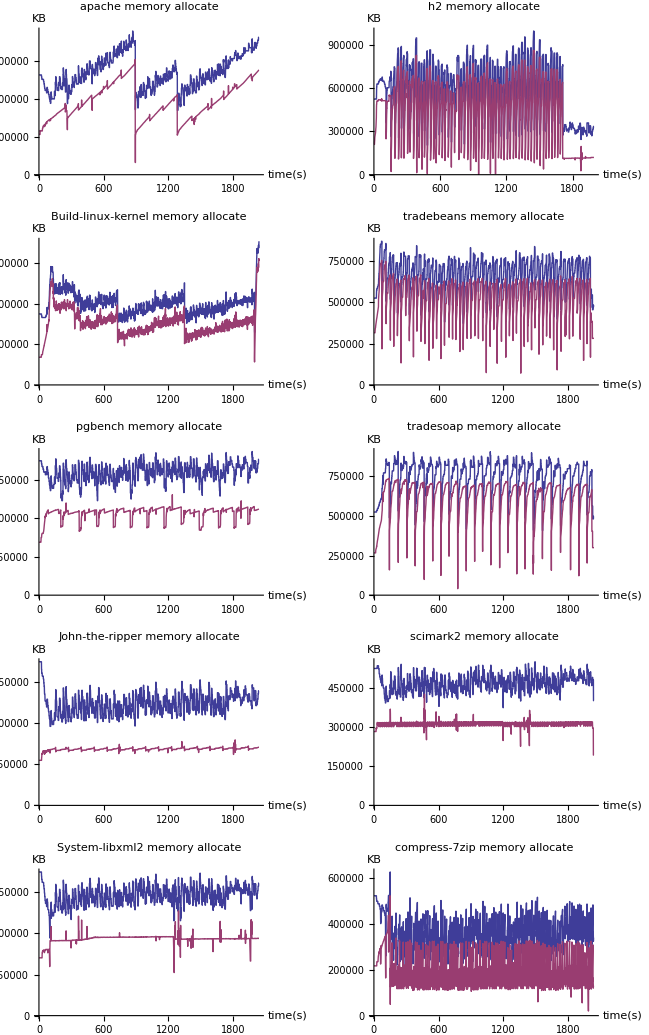

```mathematica
LineLegend[1,{"total","used"},LegendLayout->"Row"]
GraphicsGrid[Partition[Table[
ListLinePlot[{onmem[[i,All,1]],onmem[[i,All,2]]},
PlotRange->{0,All},PlotLabel->label[[i]]<>" memory allocate ",
AxesLabel->{"time(s)","KB"}
],
{i,Length[onmem]}
],2,2,1,{}]]
```

h2测试后面的平的阶段，是因为60组测试都执行完毕了。
我估计的是60组测试能够执行足够长的时间，看来应该改成120组的。
这里其实是实验失误，但是，因为高度重复性和前面有足够的数据支持，所以不想再重新测试一次了。

#### 总结

基本上内容在分析中都涉及了，在这里把结论总结一下：
1. 开启调节后，能够优化资源配置，对内存型应用有大的优化作用，对磁盘型应用有比较大的优化作用，
对CPU程序有微量的副作用。
2. 在实际虚拟机部署的时候，不推荐一台物理机上运行两台及以上的虚拟机上部署磁盘密集应用服务
3. 在实际虚拟机部署的时候，推荐一台物理机上运行多台的虚拟机上部署内存密集应用服务的时候使用调节程序。